```mathematica
NN = 3;



m0[m_] := m

m1[m_] := m ⅇ^(2 π ⅈ / NN)

m2[m_] := m ⅇ^(4 π ⅈ / NN)

σ0[m_] := ⅇ^(1/NN Log[ 1 + m^NN])Piecewise[  {{  ⅇ^(2 π ⅈ / NN),Arg[m] ≥ π /3 } , { ⅇ^(-2 π ⅈ / NN),  Arg[m] ≤ - π /3}}, 1 ]

σ1[m_] := σ0[m] ⅇ^(2 π ⅈ / NN)


σ2[m_] := σ0[m] ⅇ^(4 π ⅈ / NN)

W0[m_] :=  (- 1)/(2π)( NN σ0[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ0[m] - m ⅇ^(2 π ⅈ  j/ NN)])

W1[m_] :=  (- 1)/(2π)( NN σ1[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ1[m] - m ⅇ^(2 π ⅈ  j/ NN)])

W2[m_] :=  (- 1)/(2π)( NN σ2[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ2[m] - m ⅇ^(2π ⅈ  j/ NN)])

M10[m_] := W1[m]  -  W0[m]

M21[m_] := W2[m]  -  W1[m]

M02[m_] := W0[m]  -  W2[m]

Q10[m_]  := ⅈ ( m1[m]  -  m0[m] )

Q21[m_]  := ⅈ ( m2[m]  -  m1[m] )

Q02[m_]  := ⅈ ( m0[m]  -  m2[m] )


M10r[m_] :=   (  ⅇ^(2 π ⅈ / 3)  -  1  )W0[m]    +    ⅈ m0[m]

M21r[m_] := ⅇ^(2 π ⅈ /3) M10r[m]

M02r[m_]  := ⅇ^(2 π ⅈ /3) M21r[m]

D10r[m_, n_]  := M10r[m]   +   n Q10[m]

D21r[m_, n_]  := ⅇ^(2 π ⅈ /3) D10r[m, n]

D02r[m_, n_]  := ⅇ^(2 π ⅈ / 3)D21r[m, n]


Q20[m_]  := ⅈ ( m2[m]  -  m0[m] )


z    [a_, b_]  :=  a   +  ⅈ b

mrr[a_, b_]  :=  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  √(a^2 + b^2)

mrc[a_, b_]  :=  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  (  a^2  +  b^2  )^(1/6)
```

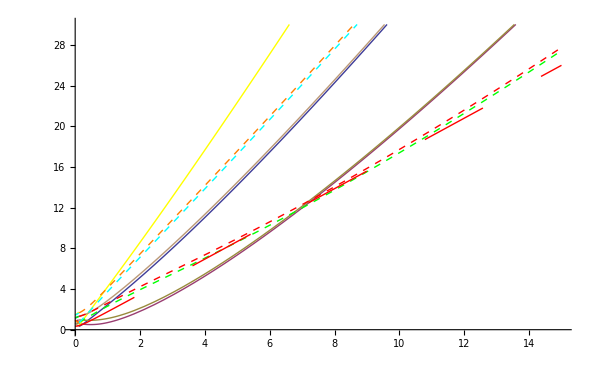

```mathematica
b = 0.2;
Plot[  {  Abs[  D10r[  z[a, b],  -1  ]  ],  Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ],
	Abs[  D10r[  z[a, b], -2  ]  ], Abs[  D10r[  z[a, b],  2  ]  ],
	Abs[  D10r[  z[a, b],  1  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  -1  ]  +  Q20[  z[a, b]  ]  ],
	Abs[  D10r[  z[a,  b], 2  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  -2  ]  +  Q20[  z[a, b]  ]  ],
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 15 },  PlotRange->{  0, 30  },
	PlotStyle->{  Thick, Thick, Thick,
				Directive[  Yellow, Thick  ],  Directive[  Lighter[Brown],  Thick], 
				Directive[Dashed, Red], Directive[ Dashed, Green], 
				Directive[Dashed, Orange, Thick], Directive[Dashed, Cyan, Thick],
				Directive[Dashing[0.08], Red, Thin]  } ]
```

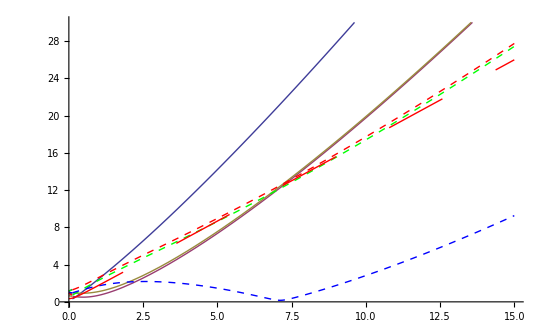

```mathematica
b = 0.2;
Plot[  {  Abs[  D10r[  z[a, b],  -1  ]  ],  Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ],
	Abs[  D10r[  z[a, b],  -1  ]  +  Q20[  z[a, b]  ]  ],Abs[  M10r[  z[a, b]  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  +  Q20[  z[a, b]  ]  ],  
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, 0, 15 },  PlotRange->{  0, 30  },
	PlotStyle->{  Thick, Thick, Thick,
				Directive[ Dashed, Green], Directive[Dashed, Blue], Directive[Dashed, Red], 
				Directive[Dashing[0.08], Red, Thin]  } ]
```

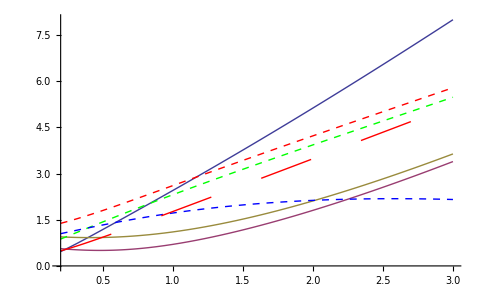

```mathematica
b = 0.2;
Plot[  {  Abs[  D10r[  z[a, b],  -1  ]  ],  Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ],
	Abs[  D10r[  z[a, b],  -1  ]  +  Q20[  z[a, b]  ]  ],Abs[  M10r[  z[a, b]  ]  +  Q20[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  +  Q20[  z[a, b]  ]  ],  
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, b, 3 },  
	PlotStyle->{  Thick, Thick, Thick,
				Directive[ Dashed, Green], Directive[Dashed, Blue], Directive[Dashed, Red], 
				Directive[Dashing[0.08], Red, Thin]  },
	AxesOrigin->{  b,  0  } ]
```

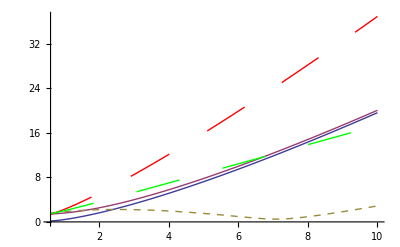

```mathematica
b = 0.6;
Plot[  {   Abs[  M10r[  z[a, b]  ]  ],  Abs[  D10r[  z[a, b],  1  ]  ], Abs[  M10r[  z[a, b]  ]  +  Q20 [  z[a, b]  ]  ],  Abs[  M10r[  z[a, b]  ]  +  Q02[  z[a, b]  ]  ], 
	Abs[  Q10[  z[a, b]  ]  ]  },
	{  a, b, 10 },  
	PlotStyle->{  Thick, Thick, Directive[Thick,  Dashed],  Directive[  Thick, Dashing[ 0.08], Red  ], 
				Directive[Dashing[0.08], Green]  },
	AxesOrigin->{  b,  0  } ]
```

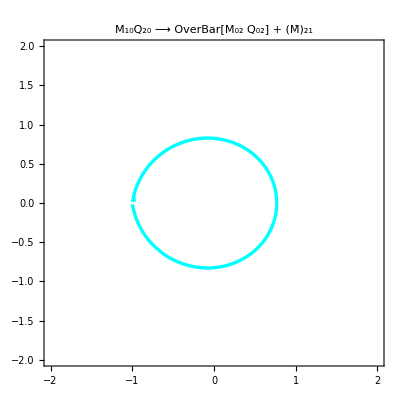

```mathematica
distance =2.0;
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrr[x, y]  ]    +    Q02[  mrr[x, y]  ]  ))/(-  ( M21r[  mrr[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_20  ⟶  OverBar[M_02 Q_02]  +  (M̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

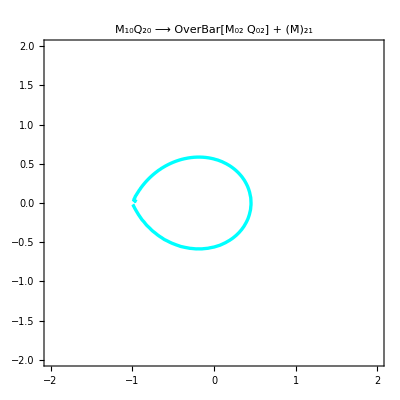

```mathematica
distance =2.0;
plotA = 
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrc[x, y]  ]    +    Q02[  mrc[x, y]  ]  ))/(-  ( M21r[  mrc[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_20  ⟶  OverBar[M_02 Q_02]  +  (M̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

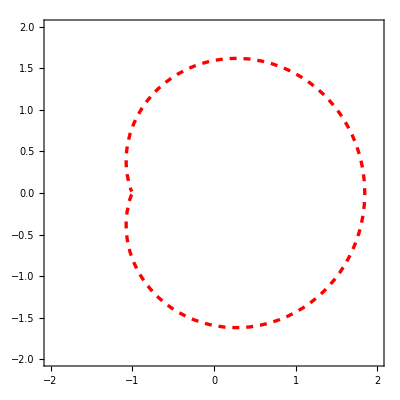

```mathematica
distance =2.0;
plotB = ContourPlot[   Evaluate[     {   Im[   M10r[  mrc[x,y]  ]/Q10[  mrc[x,y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006],    Red,    Dashed ] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

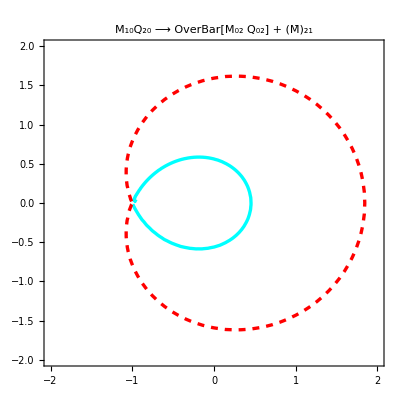

```mathematica
Show[  plotA, plotB  ]
```

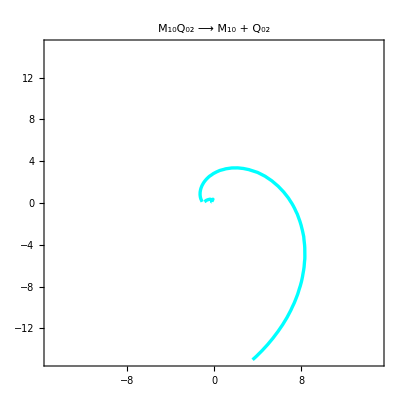

```mathematica
distance =15.0;
ContourPlot[   Evaluate[     {   Im[   M10r[  mrr[x, y]  ]/Q02[  mrr[x, y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "M_10Q_02  ⟶  M_10  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

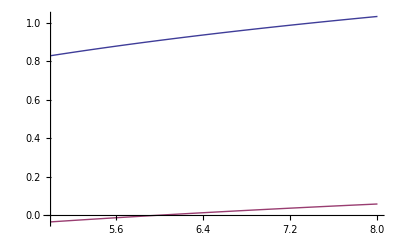

```mathematica
b  =  0.6;
Plot[  {  Re[   M10r[  z[a, b]  ]/Q02[  z[a, b]  ]   ] , Im[   M10r[  z[a, b]  ]/Q02[  z[a, b]  ]   ]   },  {  a,  5,  8  },  PlotStyle  ->  Thick  ]
```

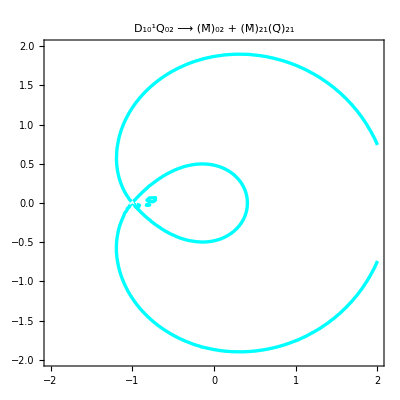

```mathematica
distance =2.0;
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrr[x, y] ]  ))/(-  (  M21r[  mrr[x, y]  ]  +  Q21[  mrr[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D_10^1Q_02  ⟶  (M̄)_02  +  (M̄)_21(Q̄)_21",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

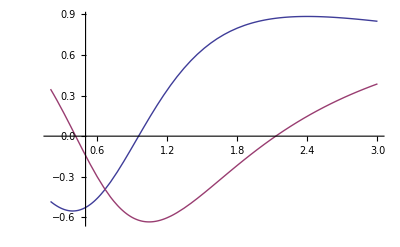

```mathematica
b  =  0.2;
Plot[  {  Re[   (-  (  M02r[  z[a, b] ]  ))/(-  (  M21r[  z[a, b]  ]  +  Q21[  z[a, b]  ]  ))   ],  Im[   (-  (  M02r[  z[a, b] ]  ))/(-  (  M21r[  z[a, b]  ]  +  Q21[  z[a, b]  ]  ))   ]  },
	{  a, 0.2, 3  }  ]
```

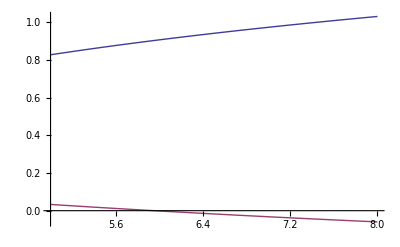

```mathematica
b  =  -0.6;
Plot[  {  Re[   D10r[  z[a, b],  1  ]/(-  Q21[  z[a, b]  ])   ] , Im[   D10r[  z[a, b],  1  ]/(-  Q21[  z[a, b]  ])   ]   },  {  a,  5,  8  },  PlotStyle  ->  Thick  ]
```

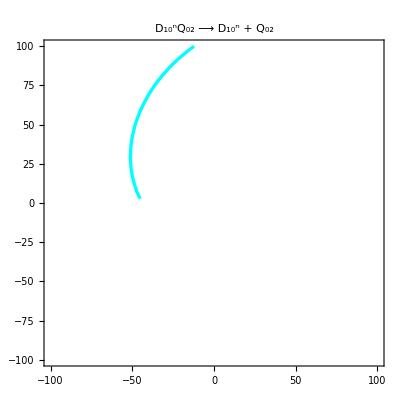

```mathematica
distance =100.0;
n  =  -1;
ContourPlot[   Evaluate[     {   Im[   D10r[  mrr[x, y],  n  ]/Q02[  mrr[x, y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D_10^nQ_02  ⟶  D_10^n  +  Q_02",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

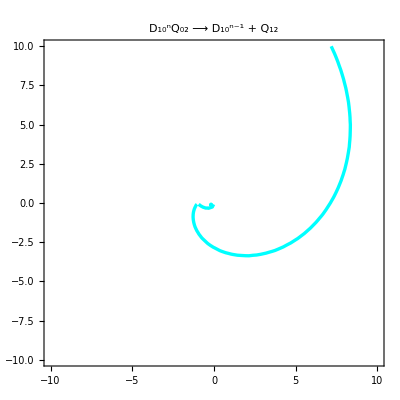

```mathematica
distance =10.0;
n  =  2;
ContourPlot[   Evaluate[     {   Im[   D10r[  mrr[x, y],  n - 1  ]/(-  Q21[  mrr[x, y]  ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },
		         PlotLabel->Style[   "D_10^nQ_02  ⟶  D_10^(n-1)  +  Q_12",  FontSize -> 24  ], 
		         LabelStyle->Directive[ FontSize->18 ] ]
```

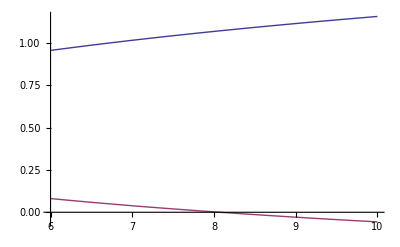

```mathematica
n  =  2;
b  =  0.6;
Plot[  {  Re[   D10r[  z[a, b],  n - 1  ]/(-  Q21[  z[a, b]  ])   ],  Im[   D10r[  z[a, b],  n - 1  ]/(-  Q21[  z[a, b]  ])   ]  },
	{  a, 6, 10  },  
	PlotStyle  ->  Thick  ]
```

## Publish

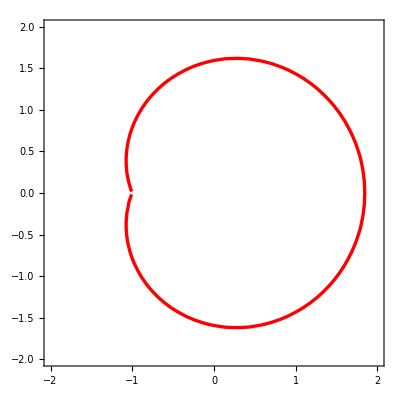

```mathematica
distance =2.0;
ContourPlot[   Evaluate[     {   Im[   M10r[  mrc[x,y]  ]/Q10[  mrc[x,y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006],    Red] },
			LabelStyle->Directive[ FontSize->18 ] ]
```

```mathematica
mre[a_, b_]  :=  ⅇ^(ⅈ 1/3 Arg[ a  +  ⅈ b ])  Exp[a^2 + b^2]
```

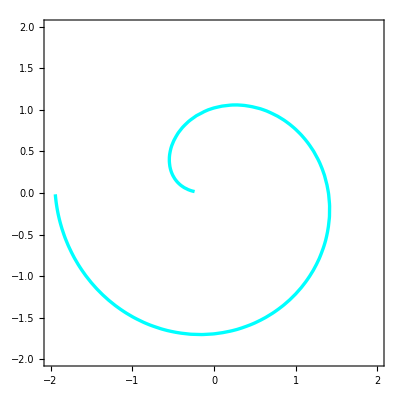

```mathematica
distance =2.0;
n  =  0;

spiral0 =
ContourPlot[   Evaluate[     {   Im[   D10r[  mre[x, y],  n  ]/Q02[  mre[x, y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },    
		         LabelStyle->Directive[ FontSize->18 ] ]
```

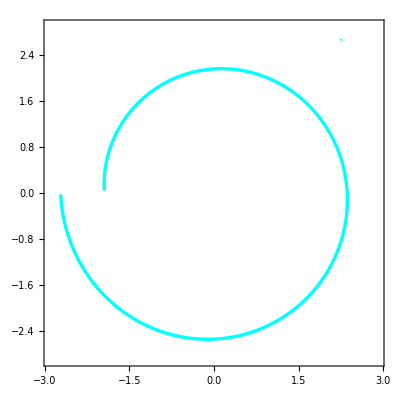

```mathematica
distance =2.9;
n  =  -1;
spiralm1 =
ContourPlot[   Evaluate[     {   Im[   D10r[  mre[x, y],  n  ]/Q02[  mre[x, y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Cyan ] },    
			LabelStyle->Directive[ FontSize->18 ] ]
```

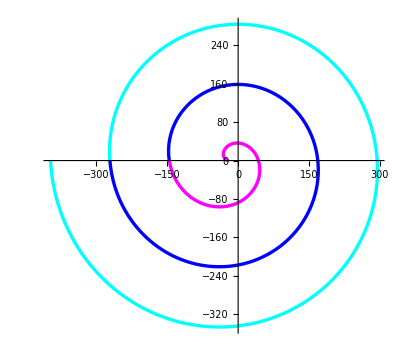

```mathematica
a = 20;
spirm[ϕ_] := {  -a - a ϕ Cos[ϕ],  a ϕ Sin[ϕ]  }
	spiralnegative =
ParametricPlot[  {  spirm[ϕ],  spirm[ϕ  +  2π],  spirm[ϕ  +  4π]  },
				{  ϕ, 0, 2π},
	   PlotStyle->{   Directive[  Thickness[0.006], Magenta ],  Directive[  Thickness[0.006],   Blue],  Directive[  Thickness[0.006], Cyan ] }]
```

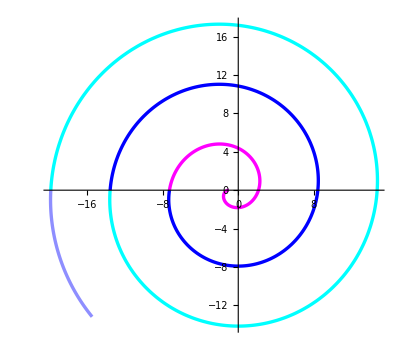

```mathematica
a = 1;
spirp[ϕ_] := {  -a - a ϕ Cos[ϕ],  - a ϕ Sin[ϕ]  }
	spiralpositive =
ParametricPlot[  {  spirp[ϕ],  spirp[ϕ  +  2π],  spirp[ϕ  +  4π], spirp[ϕ/8.5 + 6π]  },
				{  ϕ, 0, 2π},
	   PlotStyle->{   Directive[  Thickness[0.006], Magenta ],  Directive[  Thickness[0.006],   Blue],  Directive[  Thickness[0.006], Cyan ],
				Directive[  Thickness[0.006], Lighter[Lighter[Blue]]]  }  ]
```

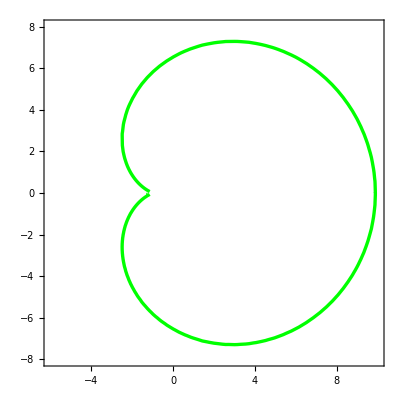

```mathematica
distance =10.0;
DQdecay = 
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrc[x, y] ]  ))/(-  (  M21r[  mrc[x, y]  ]  +  Q21[  mrc[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-6,distance },{ y,-8,  8  },
			RegionFunction->Function[  {x,y},    Abs[x]  ≥  1 ||  Abs[y]  ≥  1      ],
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Green] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

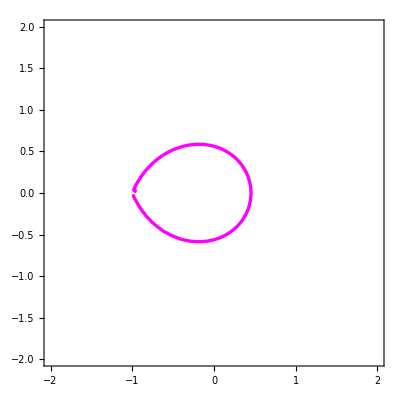

```mathematica
distance =2.0;
Vdecay = 
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrc[x, y]  ]    +    Q02[  mrc[x, y]  ]  ))/(-  ( M21r[  mrc[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006], Magenta ] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

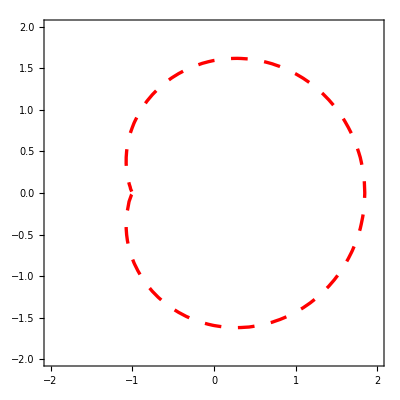

```mathematica
distance =2.0;
primarysketch = 
ContourPlot[   Evaluate[     {   Im[   M10r[  mrc[x,y]  ]/Q10[  mrc[x,y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[0.006],    Red,    Dashing[0.03] ] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

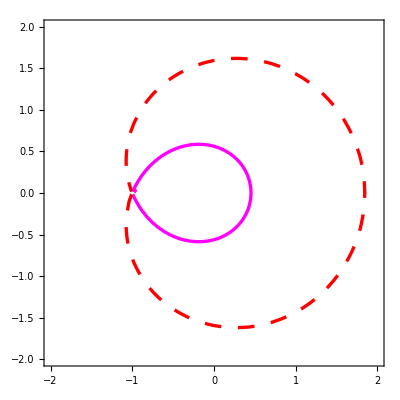

```mathematica
Show[  Vdecay, primarysketch  ]
```

```mathematica
thickness  =  0.003;
```

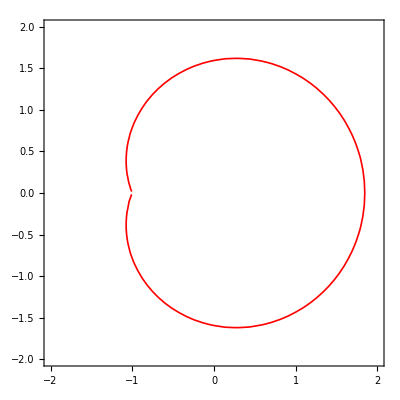

```mathematica
distance =2.0;
primary = 
ContourPlot[   Evaluate[     {   Im[   M10r[  mrc[x,y]  ]/Q10[  mrc[x,y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[thickness],    Red] },
			LabelStyle->Directive[ FontSize->18 ] ]
```

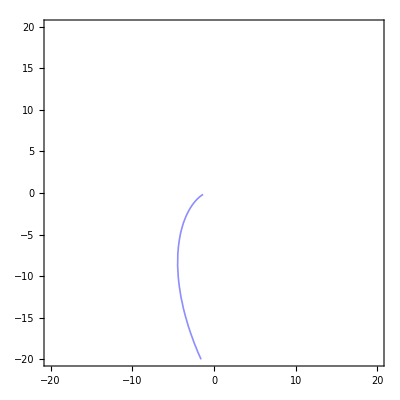

```mathematica
distance =20.0;
n  =  2;
spiralp2 = 
ContourPlot[   Evaluate[     {   Im[   D10r[  mrc[x, y],  n - 1  ]/(-  Q21[  mrc[x, y]  ])   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[thickness], Lighter[Lighter[Blue]] ] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

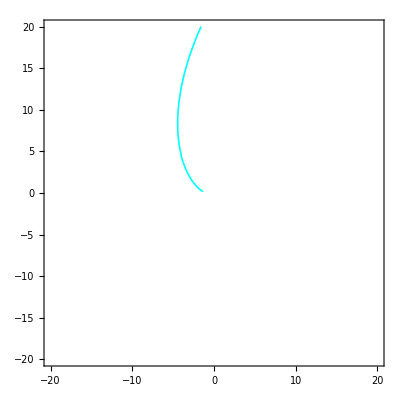

```mathematica
distance =20;
n  =  0;

spiraln0 =
ContourPlot[   Evaluate[     {   Im[   D10r[  mrc[x, y],  n  ]/Q02[  mrc[x, y]  ]   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[thickness], Cyan ] },    
		         LabelStyle->Directive[ FontSize->18 ] ]
```

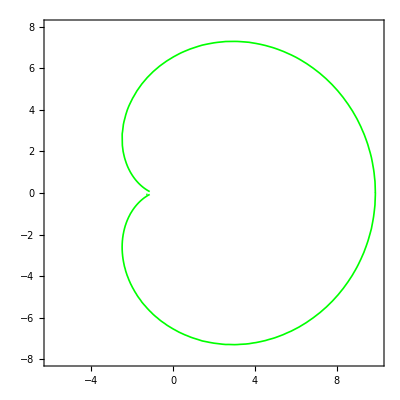

```mathematica
distance =10.0;
DQdecaythin = 
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrc[x, y] ]  ))/(-  (  M21r[  mrc[x, y]  ]  +  Q21[  mrc[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-6,distance },{ y,-8,  8  },
			RegionFunction->Function[  {x,y},    Abs[x]  ≥  1 ||  Abs[y]  ≥  1      ],
		         ContourStyle->
		      {   Directive[  Thickness[thickness], Green] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

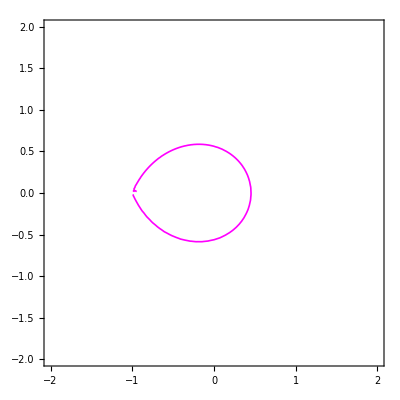

```mathematica
distance =2.0;
Vdecaythin = 
ContourPlot[   Evaluate[     {   Im[   (-  (  M02r[  mrc[x, y]  ]    +    Q02[  mrc[x, y]  ]  ))/(-  ( M21r[  mrc[x, y]  ]  ))   ]     ==      0   }     ],
                            { x,-distance,distance },{ y,-distance,distance },
		         ContourStyle->
		      {   Directive[  Thickness[thickness], Magenta ] },
		         LabelStyle->Directive[ FontSize->18 ] ]
```

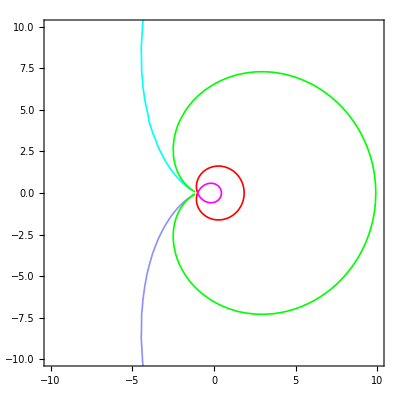

```mathematica
distance = 10;

Show[spiraln0,  spiralp2,  DQdecaythin,  primary,  Vdecaythin,
	PlotRange->{  {  -distance,  distance  },  {  -distance,  distance  }  }  ]
```